```mathematica
path = (*SystemDialogInput["FileOpen"]*)"/Users/andrey_moskvin/ImageCompression/Documents/Im189.BMP";
```

```mathematica
image = Import[path];
```

```mathematica
getImageData[image_] := ImageData[image,"Byte"];
```

```mathematica
imageFromData[data_]:=Image[data,"Byte"];
```

```mathematica
getRGB[imageData_] := Flatten[imageData,{{3}, {1}, {2}}];
```

```mathematica
combineColor[r_]:=Flatten[r,{{2},{3},{1}}];
```

```mathematica
getTransformants[layer_] := Partition[layer, {8,8},8,{1,1},{-1}];
```

```mathematica
mergeTransformants[layer_] := Flatten[layer, {{1,3},{2,4}}];
```

```mathematica
Clear[normalize]
normalize[t_]:=t/;t[[-1,-1]] ≠ -1; 
normalize[t_]:=Block[{f, result = t, last},(
f[row_]:=row/; First@row == -1 || Last@row≠-1; 
f[row_]:=row /. -1 -> (TakeWhile[row,NonNegative] // Last);

result = f /@ result;
result = Flatten[result,{{2},{1}}];
result = f /@ result;
result = Flatten[result, {{2},{1}}];

result
)];
```

```mathematica
restructure[t_] := FourierDCT[t] // IntegerPart;
```

```mathematica
reverseDCT[t_] := FourierDCT[t,3] // IntegerPart;
```

```mathematica
quantizationMatrix[step_]:=Array[1+(1 +(#1-1)+(#2-1) )*step&,{8,8}];
Quant=quantizationMatrix[2];
```

```mathematica
quantize[t_] := Quotient[t,Quant];
```

```mathematica
dequantize[t_] := Times[t,Quant];
```

```mathematica
removeSigns[t_] := Abs[t];
```

```mathematica
extractSigns[t_] := Positive[t] /.{True -> 1, False ->0};
```

```mathematica
applySigns[numbers_,signs_]:= Times[numbers,Replace[signs,0->-1,2]];
```

```mathematica
pathFinder=N ↦(
pack = {x,y,r, N} ↦{x,y,r,N};
getX = r ↦r[[1]];
getY = r ↦r[[2]];
getR = r ↦r[[3]];
getN = r ↦r[[4]];

r=pack[1,1,{{1,1}},N];

canRight = {r}↦(
If[getX[r] < getN[r], True, False]
);

canDown = {r}↦(
If[getY[r]<getN[r],True, False]
);

moveRight = {r}↦(
pack[getX[r] + 1,getY[r],Append[getR[r],{getX[r]+1,getY[r]}],getN[r]]
);

moveDown = {r}↦(
pack[getX[r], getY[r]+1,Append[getR[r],{getX[r],getY[r]+1}],getN[r]]
);

moveDiagonaleDown={r}↦(
x= getX[r];
y = getY[r];
If[x>1&&canDown[r], (
x = x-1;
y = y+1;
result=pack[x,y,Append[getR[r],{x,y}],getN[r]];
moveDiagonaleDown[result]
),
r]
);

moveDiagonaleUp={r}↦(
x= getX[r];
y = getY[r];
If[y>1&&canRight[r], (
x = x+1;
y = y-1;
result=pack[x,y,Append[getR[r],{x,y}],getN[r]];
moveDiagonaleUp[result]
),
r]
);

traverse={res}↦(
r = res;
If[canRight[r],(
r=moveRight[r];
r=moveDiagonaleDown[r];
r=If[canDown[r],moveDown[r],moveRight[r]];
r=moveDiagonaleUp[r];
traverse[r]
),(
If[canDown[r],(
r=moveDown[r];
r=moveDiagonaleDown[r];
r=moveRight[r];
r=moveDiagonaleUp[r];
traverse[r]
),r]
)]
);

r = traverse[r];
getR[r]

);
zigzagPath = pathFinder[8];
```

```mathematica
toVector={matrix}↦(
collector=pathItem↦(
element=matrix[[pathItem[[1]],pathItem[[2]]]];
element
);
Flatten[Append[{},Map[collector,zigzagPath]],{1,2}]
);

rleDecode={vector}↦(
pairs=Flatten[vector,{{2},{1}}];
createList={pair}↦(
repeatCount=pair[[2]];
repeatValue=pair[[1]];
newList={};
For[i=1,i<=repeatCount,i++,newList=Append[newList,repeatValue]];
{newList}
);
Map[createList,pairs]//Flatten
);
RunLengthEncode[x_List]:={First[#],Length[#]}&/@Split[x];

toMatrix={vector}↦(
emptyList=PadRight[{{}},{8,8}];
inserter={path,index}↦(
emptyList=ReplacePart[emptyList,{path[[1]],path[[2]]}->vector[[index]]]
);
MapIndexed[inserter,zigzagPath];
Flatten[emptyList,{{1},{2,3}}]
);

(*
Additional bits - main value list - main value bit length
*)
codingFormat=({{0, {0,1,0}}, {1, {0,1,1}}, {2, {1,0,0}}, {3, {0,0}}, {4, {1,0,1}}, {5, {1,1,0}}, {6, {1,1,1,0}}, {7, {1,1,1,1,0}}, {8, {1,1,1,1,1,0}}, {9, {1,1,1,1,1,1,0}}, {10, {1,1,1,1,1,1,1,0}}, {11, {1,1,1,1,1,1,1,1,1,0}}});
not[number_]:=1-number;

extractCategory[bits_]:=Module[{result={}},(
fullLength=Length[bits];
For[i=1,i≤Length[codingFormat],i++,(
If[(Length[codingFormat[[i,2]]]+codingFormat[[i,1]])<=fullLength,(
mainValueBits=Drop[bits,-codingFormat[[i,1]]];
If[mainValueBits==codingFormat[[i,2]],(
result=codingFormat[[i,1]];
Break[]
)];
)];
)];
result
)];

encodeDeltaDC[DC_,prevDC_]:=Module[{},(
deltaDC=DC-prevDC;
DCPower=Length[IntegerDigits[deltaDC,2]]+1;
mainCodeValue=codingFormat[[DCPower,2]];
additionalBitsCount=codingFormat[[DCPower,1]];
binaryDeltaDC=If[Positive[deltaDC],
IntegerDigits[deltaDC,2],not@IntegerDigits[deltaDC,2]];
Join[mainCodeValue,binaryDeltaDC]
)];

decodeDeltaDC[deltaDC_,previousDC_]:=Module[{result},(
category=extractCategory[deltaDC];
additionalCode=Take[deltaDC,-category];
decimalAdditionalCode=FromDigits[additionalCode,2];
positiveInterval=Interval[{2^(category-1),2^category-1}];
result=If[IntervalMemberQ[positiveInterval,decimalAdditionalCode],
decimalAdditionalCode,
-FromDigits[not@IntegerDigits[decimalAdditionalCode,2,category],2]];
result+previousDC
)];

encodeScalable[{scalableVector_}]:=Module[{scalableComponents=scalableVector},(
scalableComponents=Drop[scalableComponents,-1];
dynamicRange=BitLength[Max[scalableComponents]+1];
Map[element↦IntegerDigits[element,2,dynamicRange],scalableComponents]
)];

encodeValuable[{valuableVector_}]:=Module[{y0=(Max[valuableVector]+1),length=Length[valuableVector],result=0},(
encodeValuable[{element_,nextElement_,length_,index_}]:=Module[{mu},(
mu=If[element>nextElement,nextElement,nextElement-1];
mu*((y0-1)^(length-index))
)];
vector=Prepend[valuableVector,y0];
For[i=1,i<=length,i++,(
result+=encodeValuable[{vector[[i]],vector[[i+1]],length,i}];
result
)];
{result,y0}
)];

code[transformant_]:=Module[{},(
rleTransformant=RunLengthEncode[transformant//toVector];

NoDCtransformant=Drop[rleTransformant,1];
NoLastZeroSeries=Drop[NoDCtransformant,-1];
valuableComponents=Map[pair↦(pair[[1]]),NoLastZeroSeries,1];
scalableComponents=Map[pair↦(pair[[2]]),NoDCtransformant,1];
encodedScalable=encodeScalable[{scalableComponents}];

encodedValuable=encodeValuable[{valuableComponents}];
encodedValuable=Append[encodedValuable,Length[encodedScalable]];

{transformant[[1,1]],encodedScalable,encodedValuable}
)];
```

```mathematica
decodeScalable[{scalableVector_}]:=Module[{encodedScalable=scalableVector},(
decodedScalable=Map[element↦FromDigits[element,2],encodedScalable];
lastZeroSerie=8*8-Total[decodedScalable]-1;
Append[decodedScalable,lastZeroSerie]
)];

decodeValuable[{valuable_,dynamicRange_,valuableLength_,index_,previousY_,result_}]:=Module[{},(
If[index≤valuableLength,(
range=(dynamicRange- 1)^(valuableLength-index);
mu=valuable/range//IntegerPart;
newValuable=valuable-mu*range;
newIndex=index+1;
If[mu≥ previousY,mu+=1,mu];
newResult=Append[result,mu];
decodeValuable[{newValuable,dynamicRange,valuableLength,newIndex,mu,newResult}]
),
result
]
)];
decode[{DC_,encodedScalable_,encodedValuable_}]:=Module[{result},(
decodedScalable=decodeScalable[{encodedScalable}];

decodedValuable=
decodeValuable[Append[Join[encodedValuable,{1},{encodedValuable[[2]]}],{}]];
decodedValuable=Append[decodedValuable,0];
PrependTo[decodedValuable,DC];
PrependTo[decodedScalable,1];
result={decodedValuable,decodedScalable}//rleDecode;
result//toMatrix
)];
```

```mathematica
compressTransformant[t_] := Module[{result = t, signsMatrix},(
result = normalize[result];
result = restructure[result];
result = quantize[result];

signsMatrix = extractSigns[result];
result = removeSigns[result];
result=code[result];

{result,signsMatrix}
)];
```

```mathematica
decompressTransformant[{r_,s_}] := Module[{result = r}, (
result=decode[result];

result=applySigns[result,s];
result= dequantize[result];
result=reverseDCT[result];

result
)];
```

```mathematica
DCCoder[transformants_]:=Module[{result=transformants,i,j,z,DC,previousDC=0,encodedDC},(
maxX=Dimensions[transformants][[2]];(*x*)
maxY=Dimensions[transformants][[3]];(*y*)
maxZ=Dimensions[transformants][[1]];(*R,G,B*)

For[z=1,z≤maxZ,z++,(
For[i=1,i≤maxX,i++,(
For[j=1,j≤maxY,j++,(
If[j==1,(
previousJ=maxY;
previousI=0;
),
previousI=i;
previousJ=j-1];
DC=transformants[[z,i,j,1,1]];
If[previousI!=0,previousDC=transformants[[z,previousI,previousJ,1,1]],previousDC=0];
(*Print[{DC,previousDC}];*)
encodedDC=encodeDeltaDC[DC,previousDC];
(*Print[encodedDC];*)
result=ReplacePart[result,{z,i,j,1,1}->encodedDC];
)];
)];
)];
result
)];
DCDecoder[transformants_]:=Module[{result=transformants,i,j,z,DC,previousDC=0,decodedDC},(
maxX=Dimensions[transformants][[2]];(*x*)
maxY=Dimensions[transformants][[3]];(*y*)
maxZ=Dimensions[transformants][[1]];(*R,G,B*)

For[z=1,z≤maxZ,z++,(
For[i=1,i≤maxX,i++,(
For[j=1,j≤maxY,j++,(
If[j==1,(
previousJ=maxY;
previousI=0;
),
previousI=i;
previousJ=j-1];
DC=transformants[[z,i,j,1,1]];
If[previousI!=0,previousDC=result[[z,previousI,previousJ,1,1]],previousDC=0;];
decodedDC=decodeDeltaDC[DC,previousDC];
(*Print[{DC,previousDC}];*)
result=ReplacePart[result,{z,i,j,1,1}->decodedDC];
)];
)];
)];
result
)];
```

```mathematica
compress[image_] := Module[{result =image,dimensions = ImageDimensions[image]},(
result = getImageData[result];
result = getRGB[result];
result = getTransformants /@ result;

result = Map[compressTransformant,result,{3}];
result = DCCoder[result];

{dimensions,result}
)];
```

```mathematica
export[result_] := (
exportPath = SystemDialogInput["FileSave"];
Export[exportPath,result,"WDX"];
);
```

```mathematica
decompress[{dimensions_,r_}] := Module[{result =r},(
result = DCDecoder[result];
result = Map[decompressTransformant, result,{3}];

result = mergeTransformants /@ result;

result = combineColor[result];
result = imageFromData[result];
result = ImageCrop[result,dimensions,{Right, Bottom}];
result
)];
```

```mathematica
compressedImage=image//compress;
restoredImage = compressedImage//decompress;
```

```mathematica
image
ImageDifference[image, restoredImage]
restoredImage
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sko[image_,retoredImage_] := Module[{data, restoredData, result,f}, (
data = getImageData[image] // getRGB;
restoredData = getImageData[restoredImage] // getRGB;

result = {data, restoredData}; (*Images x Colors x Pixels x Pixels*)
result = Flatten[result, {{2},{1},{3,4}}]; (*Color x Images x Pixels*)
result = Flatten[result, {{1},{3},{2}}]; (*Color x Pixel x Images*)

f[{o_, r_}] := (o-r)^2; 
result = Map[f,result,{2}]; (*Color x Pixel diff *)
result = Map[(√((Plus@@#1)/Length[#1]))& ,result, {1}];
result
)];
δ = sko[image,restoredImage] // Mean // N
```

5.10698

```mathematica
h = 20 Log10[255/δ]
```

33.9675

```mathematica
collectBits[transformant_]:=Module[{values,signs,DCLength,ValuableLength,ScalableLength,totalLength},(
values=transformant[[1]];
DCLength=Length[values[[1]]];

If[Length[values[[2]]]≠0,
ScalableLength=Length[values[[2]]]*Length[First[values[[2]]]];,
ScalableLength=0;];

If[Length[values[[3]]]≠ 0,
ValuableLength=BitLength[values[[3,1]]]+8+8;,
ValuableLength=0];

signs=transformant[[2]];
totalLength=DCLength+ScalableLength+ValuableLength;
totalLength
)];
```

```mathematica
evaluateBitNumber[{dimensions_,r_}]:=Module[{result=r,length},(
(*Print[r[[1,1,1,1]]];
Print[collectBits[r[[1,1,1]]]];*)
length=Map[collectBits[#1]&,result,{3}]//Flatten;
length
)];
```

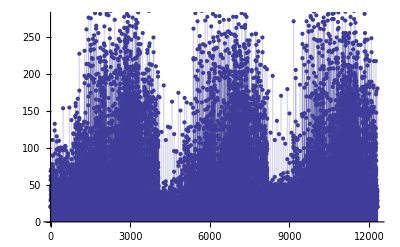

74.382

```mathematica
bitsList=compressedImage//evaluateBitNumber;
(*Total[%];
512*192;
*)
ListPlot[bitsList,Filling->Axis]
bitsList//Mean//N
```